```mathematica
base = ({{t[τ], x[τ], y[τ], z[τ]}});
η = ({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
ϕ[x_, y_] := 4 Pi (G / c^2) ρ/2 R^2 Log[(x^2 + y^2)/ R]
```

```mathematica
base[[1,2]]
```

x[τ]

```mathematica
ComputeChristoffel[h_] := Table[Sum[1/2 η[[i, l]](D[h[[l, k]], base[[1, j]]] + D[h[[l, j]], base[[1, k]]] - D[h[[k, j]], base[[1, l]]]), {l, 1, 4}], {i, 1, 4}, {j, 1, 4}, {k, 1, 4}]
```

```mathematica
h = -2 ϕ[x[τ], y[τ]]({{1, 0, 0, -2v/c}, {0, 1, 0, 0}, {0, 0, 1, 0}, {-2v/c, 0, 0, 1}});
```

```mathematica
ComputeChristoffel[h][[4]] //MatrixForm
```

(0 | (8 G π R^2 v ρ x[τ])/(c^3 (x[τ]^2+y[τ]^2)) | (8 G π R^2 v ρ y[τ])/(c^3 (x[τ]^2+y[τ]^2)) | 0
(8 G π R^2 v ρ x[τ])/(c^3 (x[τ]^2+y[τ]^2)) | 0 | 0 | -(4 G π R^2 ρ x[τ])/(c^2 (x[τ]^2+y[τ]^2))
(8 G π R^2 v ρ y[τ])/(c^3 (x[τ]^2+y[τ]^2)) | 0 | 0 | -(4 G π R^2 ρ y[τ])/(c^2 (x[τ]^2+y[τ]^2))
0 | -(4 G π R^2 ρ x[τ])/(c^2 (x[τ]^2+y[τ]^2)) | -(4 G π R^2 ρ y[τ])/(c^2 (x[τ]^2+y[τ]^2)) | 0)

```mathematica
Gammas = ComputeChristoffel[h];
```

```mathematica
eqs = Table[D[D[base[[1, i]], τ], τ] + Sum[Gammas[[i, j, k]] D[base[[1, j]], τ] D[base[[1, k]], τ], {j, 1 , 4}, {k, 1, 4}] == 0, {i, 1, 4}];
```

```mathematica
G = 6.67*10^(-11);
c = 3*10^8;
R = 1;
v = 1*10^7;
vx0 = -1*10^7;
ρ = 10^20;
x0 = 11 R;
```

```mathematica
InitConditions= { t[0] == 0, x[0] == x0, y[0] == 0, z[0] == 0, t'[0] == 1, x'[0] == vx0, y'[0] == 0, z'[0] == 0};
```

```mathematica
s = NDSolve[Join[eqs, InitConditions], {t[τ], x[τ], y[τ], z[τ]}, {τ, 0, Abs[(x0 - R)/vx0]}]
```

{{t[τ]→InterpolatingFunction[…][τ],x[τ]→InterpolatingFunction[…][τ],y[τ]→InterpolatingFunction[…][τ],z[τ]→InterpolatingFunction[…][τ]}}

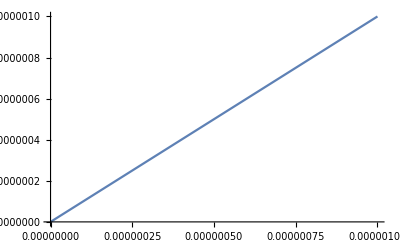

```mathematica
Plot[{Evaluate[t[τ]/.s]},{τ,0,Abs[(x0 - R)/vx0]},PlotRange->All]
```

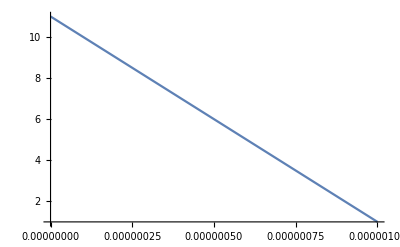

```mathematica
Plot[{Evaluate[x[τ]/.s]},{τ,0,Abs[(x0 - R)/vx0]},PlotRange->All]
```

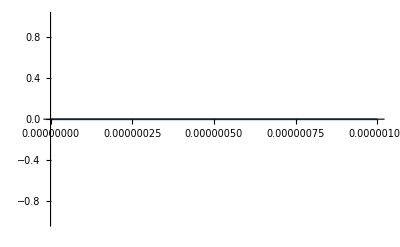

```mathematica
Plot[{Evaluate[y[τ]/.s]},{τ,0,Abs[(x0 - R)/vx0]},PlotRange->All]
```

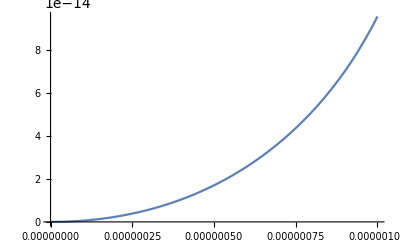

```mathematica
Plot[{Evaluate[z[τ]/.s]},{τ,0,Abs[(x0 - R)/vx0]},PlotRange->All]
```

```mathematica
Clear[h, c, ρ, vx0, Ω, κ, vy0]
```

```mathematica
h = 4 κ c ρ Ω({{0, -y[τ], x[τ], 0}, {-y[τ], 0, 0, 0}, {x[τ], 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Gammas = ComputeChristoffel[h];
```

```mathematica
Gammas[[4]] // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
eqs = Table[D[D[base[[1, i]], τ], τ] + Sum[Gammas[[i, j, k]] D[base[[1, j]], τ] D[base[[1, k]], τ], {j, 1 , 4}, {k, 1, 4}] == 0, {i, 1, 4}];
```

```mathematica
FullSimplify[eqs] // MatrixForm
```

(t''[τ]==0
8 c κ ρ Ω t'[τ] y'[τ]==x''[τ]
8 c κ ρ Ω t'[τ] x'[τ]+y''[τ]==0
z''[τ]==0)

```mathematica
κ = 1;
c = 3*10^8;
ρ = 10^20;
Ω = 10^10;
vx0 = 2;
vy0 = -1;
```

```mathematica
InitConditions= { t[0] == 0, x[0] == 0, y[0] == 0, z[0] == 0, t'[0] == 1, x'[0] == vx0, y'[0] == vy0, z'[0] == 0};
```

```mathematica
s = NDSolve[Join[eqs, InitConditions], {t[τ], x[τ], y[τ], z[τ]}, {τ, 0, 10^(-37)}]
```

{{t[τ]→InterpolatingFunction[…][τ],x[τ]→InterpolatingFunction[…][τ],y[τ]→InterpolatingFunction[…][τ],z[τ]→InterpolatingFunction[…][τ]}}

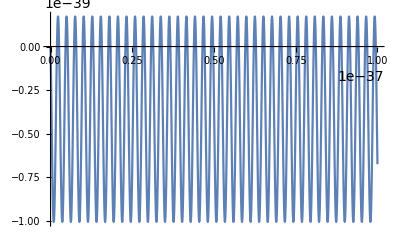

```mathematica
Plot[{Evaluate[y[τ]/.s]},{τ,0, 10^(-37)},PlotRange->All]
```

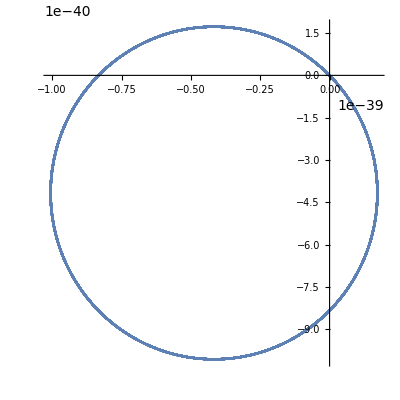

```mathematica
ParametricPlot[Evaluate[{x[τ], y[τ]}/.s], {τ, 0, 10^(-37)}, AspectRatio->1]
```

```mathematica
FullSimplify[DSolve[{x''[t] - α y'[t] == 0, y''[t] + α x'[t] == 0, x[0] == 0, y[0] == 0, x'[0] == vx0, y'[0] == vy0}, {x[t], y[t]}, t]]
```

{{x[t]→(vy0-vy0 Cos[t α]+vx0 Sin[t α])/α,y[t]→(vx0 (-1+Cos[t α])+vy0 Sin[t α])/α}}

```mathematica
α = 8 c κ ρ Ω
α = 1
```

2400000000000000000000000000000000000000

1

```mathematica
x[t_]:=(vy0-vy0 Cos[t α]+vx0 Sin[t α])/α
y[t_]:=(vx0 (-1+Cos[t α])+vy0 Sin[t α])/α
```

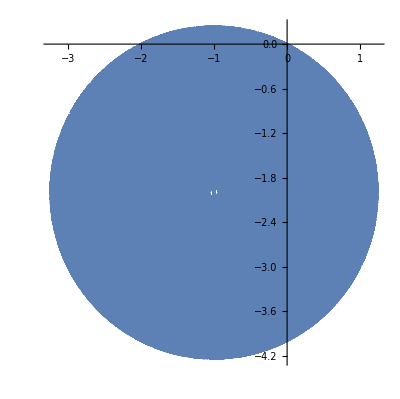

```mathematica
ParametricPlot[{x[t], y[t]}, {t, 0, 200000}]
```

```mathematica
(Abs[vx0] + Abs[vy0])/α
```

3

```mathematica
FullSimplify[x[t]^2 + y[t]^2]
```

((vx0^2+vy0^2) Sin[4 c t κ ρ Ω]^2)/(16 c^2 κ^2 ρ^2 Ω^2)

```mathematica
Sqrt[16]
```

4

```mathematica
Clear[x, y]
```

```mathematica
N[2 Sqrt[vx0^2 + vy0^2]/( α)]
```

4.47214

```mathematica
dssq = - c^2 dt^2 + dr^2 + r^2 dtheta^2 + r^2 Ω^2 dt^2 + r^2 Ω dtheta dt + dz^2
```

-c^2 dt^2+dz^2+(2 dx+2 dy)^2/(4 (x^2+y^2))+(dy x-dx y)^2/(x^2+y^2)+dt (dy x-dx y) Ω+dt^2 (x^2+y^2) Ω^2

```mathematica
r = Sqrt[x^2 + y^2];
dr = (2 dx + 2 dy)/(2 Sqrt[x^2 + y^2]);
dtheta = (x dy - y dx)/(x^2 + y^2);
```

```mathematica
Collect[Expand[dssq], {dt^2, dx^2, dy^2, dz^2}]
```

dz^2+dy^2 (1/(x^2+y^2)+x^2/(x^2+y^2))+dx dy (2/(x^2+y^2)-(2 x y)/(x^2+y^2))+dx^2 (1/(x^2+y^2)+y^2/(x^2+y^2))+dt (dy x Ω-dx y Ω)+dt^2 (-c^2+x^2 Ω^2+y^2 Ω^2)

```mathematica
h = ({{(x[τ]^2 + y[τ]^2)Ω^2, Ω y[τ]/2, - Ω x[τ]/2, 0}, {Ω y[τ]/2, 0, 0, 0}, {-Ω x[τ]/2, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Gammas = ComputeChristoffel[h];
```

```mathematica
Gammas[[3]] // MatrixForm
```

(-Ω^2 y[τ] | -Ω/2 | 0 | 0
-Ω/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
eqs = Table[D[D[base[[1, i]], τ], τ] + Sum[Gammas[[i, j, k]] D[base[[1, j]], τ] D[base[[1, k]], τ], {j, 1 , 4}, {k, 1, 4}] == 0, {i, 1, 4}];
```

```mathematica
FullSimplify[eqs] // MatrixForm
```

(2 Ω^2 t'[τ] (x[τ] x'[τ]+y[τ] y'[τ])==t''[τ]
Ω t'[τ] (Ω x[τ] t'[τ]-y'[τ])==x''[τ]
Ω t'[τ] (Ω y[τ] t'[τ]+x'[τ])==y''[τ]
z''[τ]==0)